# Math 223: Homework 5

Hardeep Bassi

03/08/2023

## Problem 1

Find the first three terms in the local behavior as of a particular solution  to .

First we check the homogenous solution by assuming . This means we seek the solution to , which has known solution . With this solution, however, we see that our assumption is not held true:

```mathematica
Limit[x^(-3)/x*E^(-x^2/2), x->0, Direction->FromAbove]
```

∞

Since this does not hold, we now try . This means that we seek the solution to . This has known solution of . Checking our assumption now, we see that:

```mathematica
Limit[x*(-1/2)*(x^(-2))/x^-3, x->0, Direction->FromAbove]
```

0

Now we seek a correction term  as , where  as .

```mathematica
y'[x]+x y[x]==x^-3 /. y -> Function[x,-1/2 x^-2+c[x]]//FullSimplify
```

2 (x c[x]+c'[x])==1/x

Here we make the assumption that  as , which yields  as . This has known solution . To verify our assumption, we see that:

```mathematica
Limit[(x*(Log[x]/2))/((1/2)*x^(-1)), x->0, Direction->FromAbove]
```

0

This means we have that  as . To find the third term, we add a correction to yield   as .

```mathematica
y'[x]+x y[x]==x^-3 /. y -> Function[x,-1/2 x^-2+Log[x]/2+ d[x]]//FullSimplify // Expand
```

2 x d[x]+x Log[x]+2 d'[x]==0

Taking   as yields the asymptotic relation of .

```mathematica
DSolve[d'[x]==-(1/2)*x*Log[x], d[x], x] // FullSimplify // Expand
```

{{d[x]→x^2/8+C[1]-1/4 x^2 Log[x]}}

To verify our assumption, we see that:

```mathematica
Limit[(x^2/8-1/4 x^2 Log[x])/(Log[x]/2), x->0, Direction->FromAbove]
```

0

Hence, we see that the first three terms are given as .

## Problem 2

Find the leading behavior of  as .

Taking a series expansion of the integrand and then integrating, allows us to obtain the leading behavior as

```mathematica
Integrate[ Collect[Series[E^(-x*t)/(1+t^2),{x,0,5}],x],{t,0,1}]//Expand
```

π/4+x^2/2-(π x^2)/8-x^3/12-x^4/36+(π x^4)/96+x^5/480-1/2 x Log[2]+1/12 x^3 Log[2]-1/480 x^5 Log[4]

We can compare how well this works against the built-in Mathematica numerical integration function as:

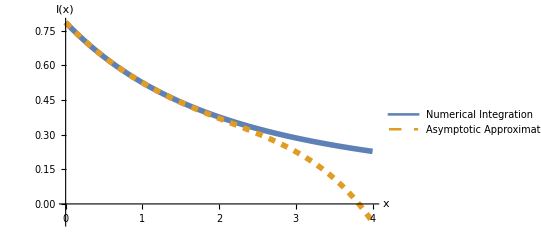

```mathematica
Plot[{NIntegrate[E^(-x*t)/(1+t^2),{t,0,1}],π/4+x^2/2-(π x^2)/8-x^3/12-x^4/36+(π x^4)/96+x^5/480-1/2 x Log[2]+1/12 x^3 Log[2]-1/480 x^5 Log[4]},{x,0,4},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```

## Problem 3

Find the asymptotic series for

First, we perform the substitution given by . This means our integral turns into: . Taking a series expansion on this yields and then integrating allows us to obtain the asymptotic series:

```mathematica
Integrate[Collect[Series[4*s^2*E^(-s^4),{s,0,10}],s],{s,0,x^(1/4)}]
```

(4 x^(3/4))/3-(4 x^(7/4))/7+(2 x^(11/4))/11

Here, we validate against Mathematica’s built-in numerical integration:

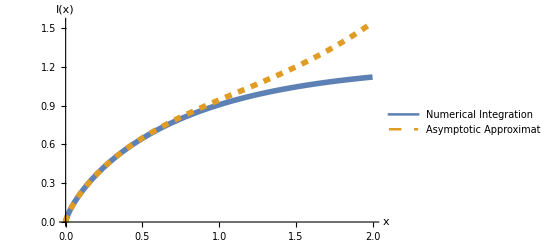

```mathematica
Plot[{NIntegrate[t^(-1/4)*E^(-t),{t,0,x}],(4 x^(3/4))/3-(4 x^(7/4))/7+(2 x^(11/4))/11},{x,0,2},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```